```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"<>"1\\";
```

```mathematica
SetDirectory[dir1];
```

```mathematica
list=FileNames["*.jpg"];
```

```mathematica
tfinal=Length[list];
```

```mathematica
For[time=1, time<tfinal, time=time+1,
backgroundfile=dir1<>"image001.jpg";
pictnumber=ToString[time+1];
If[time<9,file=dir1<>"image00"<>pictnumber<>".jpg",file=dir1<>"image0"<>pictnumber<>".jpg"];
img1=Import[file];
Bkg=Import[backgroundfile];
imgD=ImageDifference[img1,Bkg];
imgDRBinary=Binarize[imgD];
databn=ImageData[imgDRBinary];
{r,g,b}=ColorSeparate[imgD];
{w,h}=ImageDimensions[imgD];
data=ImageData[r,"Byte"];
datag=ImageData[g,"Byte"];
datab=ImageData[b,"Byte"];
For[i=1,i<h+1,i=i+1,	
rb[i,time]=Dot[databn[[i]],Table[1,{i,1,w}]]/2;
rbd[i,time]=If[rb[i,time]≠0, rb[i,time]*2,1];
bRed[i,time]=Dot[databn[[i]],data[[i]]];
bGreen[i,time]=Dot[databn[[i]],datag[[i]]];
bBlue[i,time]=Dot[databn[[i]],datab[[i]]];

CbRed[i,time]=bRed[i,time]/rbd[i,time];
CbGreen[i,time]=bGreen[i,time]/rbd[i,time];
CbBlue[i,time]=bBlue[i,time]/rbd[i,time];
] ;

For[j=1,j<w+1,j=j+1,	
ra[j,time]=Dot[databn[[All,j]],Table[1,{i,1,h}]]/2;
rad[j,time]=If[ra[j,time]≠0, ra[j,time]*2,1];
aRed[j,time]=Dot[databn[[All,j]],data[[All,j]]];
aGreen[j,time]=Dot[databn[[All,j]],datag[[All,j]]];
aBlue[j,time]=Dot[databn[[All,j]],datab[[All,j]]];

CaRed[j,time]=aRed[j,time]/rad[j,time];
CaGreen[j,time]=aGreen[j,time]/rad[j,time];
CaBlue[j,time]=aBlue[j,time]/rad[j,time];
];

Area[time]=Dot[Table[rb[i,time],{i,1,h}],Table[1,{i,1,h}]];
maxb[time]=Max[Table[rb[i,time],{i,1,h}]];

TotalRed[time]=Dot[Table[bRed[i,time],{i,1,h}],Table[1,{i,1,h}]];
TotalGreen[time]=Dot[Table[bGreen[i,time],{i,1,h}],Table[1,{i,1,h}]];
TotalBlue[time]=Dot[Table[bBlue[i,time],{i,1,h}],Table[1,{i,1,h}]];

CtRed[time]=TotalRed[time]/Area[time];
CtGreen[time]=TotalGreen[time]/Area[time];
CtBlue[time]=TotalBlue[time]/Area[time];

For[i=h,i>0,i=i-1,
If[rb[i,time]/maxb[time]>0.01,fp[time]=i;i=0]]


]
```

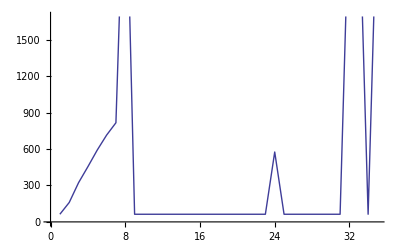
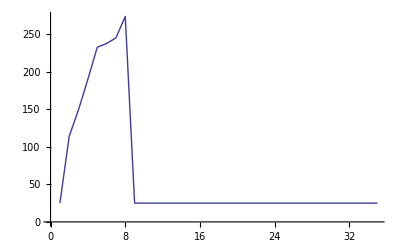
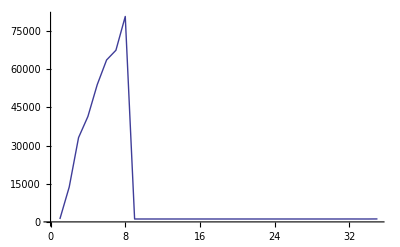
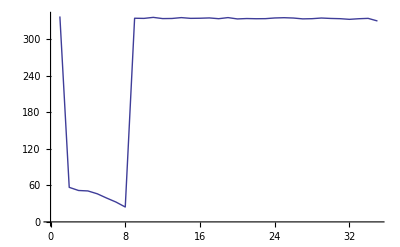
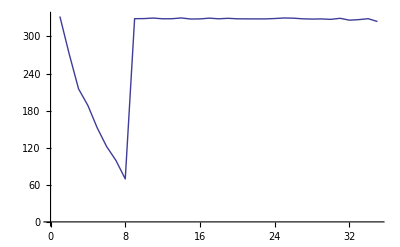
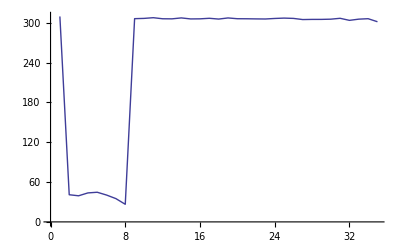

```mathematica
{gfrontp,gradius,gArea,gCred,gCgreen,gCblue}={ 
ListLinePlot[Table[fp[time],{time,1,tfinal}]],
ListLinePlot[Table[maxb[time],{time,1,tfinal}]],
ListLinePlot[Table[Area[time],{time,1,tfinal}]],
ListLinePlot[Table[CtRed[time],{time,1,tfinal}]],
ListLinePlot[Table[CtGreen[time],{time,1,tfinal}]],
ListLinePlot[Table[CtBlue[time],{time,1,tfinal}]]
}
```